```mathematica
Means={0.0,1.9061 10^-6,-9.5122 10^-5,-0.0048434,0.026466,0.11993,0.24097, 0.51647, 0.81273, 2.6582, 4.2137, 5.7821}
```

{0.,1.9061×10^-6,-0.000095122,-0.0048434,0.026466,0.11993,0.24097,0.51647,0.81273,2.6582,4.2137,5.7821}

```mathematica
sd={0.0, 0.01,0.1, 0.25, 0.5, 0.75, 1.0,1.5, 2.0, 5.0,7.5, 10.0}
```

{0.,0.01,0.1,0.25,0.5,0.75,1.,1.5,2.,5.,7.5,10.}

```mathematica
uncert = {0.0,3.1637 10^-6,3.1804 10^-5,8.2168 10^-5,0.00015184,0.0002137,0.00027547,0.00040134,0.00052957,0.0013062,0.0019564,0.0026082}
```

{0.,3.1637×10^-6,0.000031804,0.000082168,0.00015184,0.0002137,0.00027547,0.00040134,0.00052957,0.0013062,0.0019564,0.0026082}

```mathematica
data = Transpose[{sd,Means}];
```

```mathematica
data//MatrixForm
```

(0. | 0.
0.01 | 1.9061×10^-6
0.1 | -0.000095122
0.25 | -0.0048434
0.5 | 0.026466
0.75 | 0.11993
1. | 0.24097
1.5 | 0.51647
2. | 0.81273
5. | 2.6582
7.5 | 4.2137
10. | 5.7821)

## Fits Formulae

```mathematica
line = a+b x
```

a+b x

```mathematica
lineFit[d_]:=FindFit[d,line,{a,b},x]
```

```mathematica
parabola = a x^2+b x + c
```

c+b x+a x^2

```mathematica
paraFit[d_] := FindFit[d,parabola,{a,b,c},x]
```

```mathematica
exponential = a ⅇ^(b x)+c
```

c+a ⅇ^(b x)

```mathematica
expFit[d_] := FindFit[d, exponential, {a,b,c},x]
```

```mathematica
expFit[data]
```

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{a→7233.4,b→0.000163664,c→-7237.66}

```mathematica
ln = a Log[b/x]+c
```

c+a Log[b/x]

```mathematica
lnFit[d_]:= FindFit[d, ln,{a,b,c},x]
```

```mathematica
lnFit[data]
```

Power::infy: Infinite expression 1/0. encountered.

FindFit::nrlnum: The function value {∞, 6.42385, 34.1594, 2.39114, 1.66668, 1.16775, 0.75903, 0.0780649, -0.505877, -3.26764, « 2 »} is not a list of real numbers with dimensions {12} at {a, b, c} = {1., 1., 1.}.

FindFit[{{0.,0.},{0.01,-0.818683},{0.1,-30.8568},{0.25,-0.0048434},{0.5,0.026466},{0.75,0.11993},{1.,0.24097},{1.5,0.51647},{2.,0.81273},{5.,2.6582},{7.5,4.2137},{10.,5.7821}},c+a Log[b/x],{a,b,c},x]

## Analysis

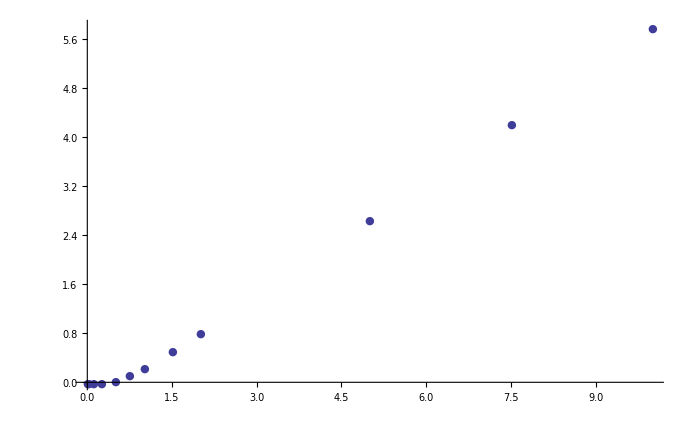

```mathematica
ListPlot[data, PlotMarkers->{●,Medium}, PlotRange->All]
```

```mathematica
line
```

a+b x

```mathematica
lAll = line/.lineFit[data]
```

-0.203917+0.587649 x

```mathematica
l6 = line/.lineFit[data[[7;;12]]]
```

-0.40635+0.617121 x

```mathematica
p6 =parabola/.paraFit[data[[1;;6]]]
```

0.00323157-0.136096 x+0.385475 x^2

```mathematica
p7 = parabola/.paraFit[data[[1;;7]]]
```

0.00243675-0.11991 x+0.359842 x^2

```mathematica
pAll =parabola/.paraFit[data]
```

-0.13006+0.475514 x+0.0122602 x^2

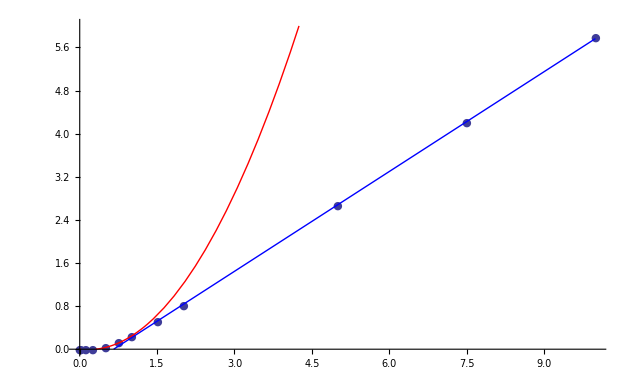

```mathematica
Show[ListPlot[data, PlotMarkers->{●,Medium}, PlotRange->All],Plot[{ l6,p7},{x,0,10},PlotStyle->{{Blue},{Red}}, PlotRange->{0,6}]]
```

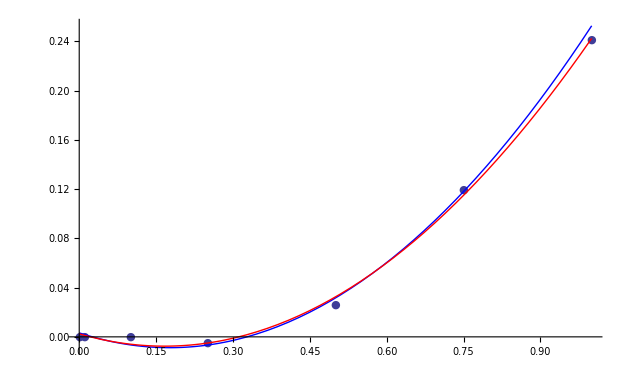

```mathematica
Show[ListPlot[data[[1;;7]], PlotMarkers->{●,Medium}, PlotRange->All],Plot[{ p6,p7},{x,0,1},PlotStyle->{{Blue},{Red}}]]
```

```mathematica
Length[data]
```

12

```mathematica
data[[7;;12]]
```

{{1.,0.24097},{1.5,0.51647},{2.,0.81273},{5.,2.6582},{7.5,4.2137},{10.,5.7821}}

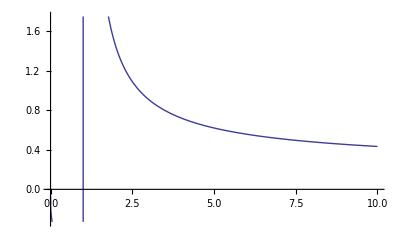

```mathematica
Plot[1/Log[x],{x,0,10}]
```